#### Rb Vapor Pressure From (https://www2.iap.tuwien.ac.at/www/surface/vapor_pressure) Nozzle Tolerance Calcs

```mathematica
DisSamp=16.8; 
RadTube =.2;
RadNozzleFlange = .75;
MaxAng = ArcTan[DisSamp/RadTube];
MaxAngDegrees = MaxAng/Degree;
MaxBeamDivergence = 90-MaxAngDegrees;
MaxTol = RadNozzleFlange/Tan[MaxAng];
Print["MaxBeamDivergence: ",MaxBeamDivergence,"°"]
Print["MaxTolerance: ",MaxTol,"(in)"]
```

MaxBeamDivergence: 0.68206°

MaxTolerance: 0.00892857(in)

#### Beam Divergence Non Collimated

```mathematica
RbConeAngle = Pi/2-MaxAng;(*max angle the triangle that when rotated makes the cone can be before hitting the smallest inner diameter tube and sticking*)
σ=1.768  (*g/cm^3 Density argon at 20K Weinstein*);
Mar=39.948 (*Molar Mass Argon*);
NAr = σ/1 1/1000 1/Mar (6.023*^23)/1 (*# Ar in mm^3*);
Par= 10 (*torr, Pressue Ar by cold head*);
Prb=Par 10^13/NAr ;
VolumeRbCone = 1/3 Pi RadTube^3 DisSamp;
VolumeArHemisphere = 2/3 Pi DisSamp^3;
Par/Prb;
 Solve[VolumeArHemisphere/(VolumeRbCone*RbAd)==1,RbAd];(*Adjustment to Rb pressure to maintain ratio*)
RbAdj = 70560;
Print["Ratio Volume RbCone to Volume Ar Hemisphere:",RbAdj, "(just volume, not ratio of # particles"]
Print["New pressure needed to maintain ratio:",Prb*RbAdj]
ConeSolidAngle = (Pi RadTube^2)/(RadTube^2+DisSamp^2);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Ratio Volume RbCone to Volume Ar Hemisphere:70560(just volume, not ratio of # particles

New pressure needed to maintain ratio:0.264703

```mathematica
(*~520 K / 250 C*)
```

#### Beam Divergence visualization

```mathematica
(*Define the parameters for the cone*)
maxRadius=RadTube; (*R,radius of the base*)
height=DisSamp; (*h,height of the cone*)
slope=height/maxRadius; (*k,slope of the cone*)

(*Parametric equation for the cone*)
cone=ParametricPlot3D[{r Cos[theta],r Sin[theta],slope*r},{r,0,maxRadius},{theta,0,2 Pi},Mesh->None,PlotStyle->Directive[Orange,Opacity[0.7]],PlotRange->All,Boxed->False,Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"3D Plot of a Cone"];

(*dispaly cone and hemisphere*)
RbCone = ParametricPlot3D[{r Cos[theta],r Sin[theta],slope*r},{r,0,DisSamp},{theta,0,2 Pi},Mesh->None,PlotStyle->Directive[Red,Opacity[0.7]],PlotRange->All,Boxed->False,Axes->True,AxesLabel->{"x","y","z"},PlotLabel->"3D Plot of a Cone"];

ArHemisphere = SphericalPlot3D[DisSamp,{θ,0,Pi/2},{ϕ,0,2Pi},Mesh->None,PlotStyle->Directive[Blue,Opacity[0.7]],PlotRange->All,Boxed->False];

Show[RbCone,ArHemisphere,PlotRange->{{-DisSamp,DisSamp},{-DisSamp,DisSamp},{0,DisSamp}}]
```

-Graphics3D-

#### MicroCapilarry Array Tilt to avoid tolerance issues

Tilt angle: 0 degrees

Length of the overlapping region at y = h: 0.4 in

Length of the top edge of the green cone: 0.4 in

Percentage of overlap length relative to the green top edge: 100. %

Percentage of Rb lost to walls: 14.2654 %

Rememeber this is a 1D simplifcation of a 3D system

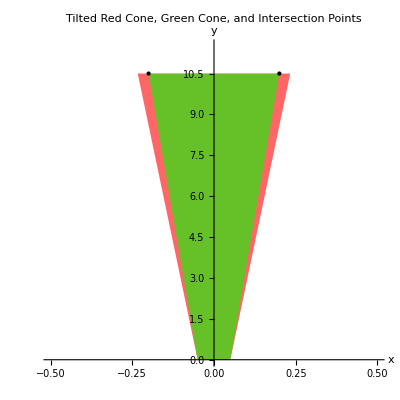

```mathematica
(*Define parameters*)
nozzleRadius=0.1/2; (*Radius at the nozzle*)
divergenceAngleDegrees=1; (*Beam divergence angle in degrees*)
divergenceAngleRadians=divergenceAngleDegrees*Pi/180; (*Convert to radians*)
h=10.5; (*Distance the beam travels after the nozzle*)
tiltAngleDegrees=0; (*Tilt angle in degrees,can be changed*)
tiltAngleRadians=tiltAngleDegrees*Pi/180; (*Convert to radians*)

(*Calculate the top width of the truncated triangle for the red cone*)
topWidthRed=2*(nozzleRadius+h*Tan[divergenceAngleRadians]);

(*Coordinates for the original truncated triangle for the red cone*)
bottomLeft={-nozzleRadius,0};
bottomRight={nozzleRadius,0};
topLeftRed={-topWidthRed/2,h};
topRightRed={topWidthRed/2,h};

(*Rotation matrix for the tilt*)
rotationMatrix={{Cos[tiltAngleRadians],-Sin[tiltAngleRadians]},{Sin[tiltAngleRadians],Cos[tiltAngleRadians]}};

(*Apply rotation to the top points of the red cone*)
topLeftTilted=rotationMatrix.{topLeftRed[[1]],topLeftRed[[2]]};
topRightTilted=rotationMatrix.{topRightRed[[1]],topRightRed[[2]]};

(*Top radius of the green cone, based on smallest ID we pass through*)
greenConeTopRadius=0.2;

(*Coordinates for the green cone*)
greenTopLeft={-greenConeTopRadius,h};
greenTopRight={greenConeTopRadius,h};

(*Function to calculate overlapping length for a given tilt angle*)
overlappingLengthFunction[tiltAngleDegrees_]:=Module[{tiltAngleRadians,topLeftTilted,topRightTilted,xIntersectionLeft,xIntersectionRight,overlappingLength},(*Convert tilt angle to radians*)tiltAngleRadians=tiltAngleDegrees*Pi/180;
(*Rotation matrix for the tilt*)
rotationMatrix={{Cos[tiltAngleRadians],-Sin[tiltAngleRadians]},{Sin[tiltAngleRadians],Cos[tiltAngleRadians]}};
(*Apply rotation to the top points of the red cone*)
topLeftTilted=rotationMatrix.{topLeftRed[[1]],topLeftRed[[2]]};
topRightTilted=rotationMatrix.{topRightRed[[1]],topRightRed[[2]]};
(*Calculate the intersection points of the top edges*)
xIntersectionLeft=Max[-greenConeTopRadius,Min[topLeftTilted[[1]],topRightTilted[[1]]]];
xIntersectionRight=Min[greenConeTopRadius,Max[topLeftTilted[[1]],topRightTilted[[1]]]];
(*Ensure the intersection points are within the bounds of the green cone's top edge*)
xIntersectionLeft=Max[xIntersectionLeft,-greenConeTopRadius];
xIntersectionRight=Min[xIntersectionRight,greenConeTopRadius];
(*Calculate the length of the overlapping region*)overlappingLength=Max[0,xIntersectionRight-xIntersectionLeft];
(*Return the overlapping length*){overlappingLength,xIntersectionLeft,xIntersectionRight}];

(*Calculate the overlapping length for the given tilt angle*)
overlappingLength=overlappingLengthFunction[tiltAngleDegrees][[1]];

(*Length of the top edge of the green cone*)
greenTopLength=2*greenConeTopRadius; (*This is the full diameter,which is twice the radius*)

(*Calculate the percentage of overlap relative to the green top edge length*)
percentageOverlapLength=(overlappingLength/greenTopLength)*100;

(*Calculate the percentage of Rb lost to walls*)
percentageRbLost = ((topWidthRed - overlappingLength)/topWidthRed)*100;

(*Print results*)
Print["Tilt angle: ",tiltAngleDegrees," degrees"];
Print["Length of the overlapping region at y = h: ",overlappingLength," in"];
Print["Length of the top edge of the green cone: ",greenTopLength," in"];
Print["Percentage of overlap length relative to the green top edge: ",percentageOverlapLength," %"];
Print["Percentage of Rb lost to walls: ",percentageRbLost," %"];
Print["Rememeber this is a 1D simplifcation of a 3D system"];

(*Visualization*)
(*Define the green cone polygon*)
greenCone=Graphics[{Green,Opacity[0.6],Polygon[{bottomLeft,bottomRight,greenTopRight,greenTopLeft}]}];

(*Define the tilted red cone polygon*)
tiltedTriangle=Graphics[{Red,Opacity[0.6],Polygon[{bottomLeft,bottomRight,topRightTilted,topLeftTilted}]}];

(*Calculate correct intersection points*)
xIntersectionLeftPlot=overlappingLengthFunction[tiltAngleDegrees][[2]];
xIntersectionRightPlot=overlappingLengthFunction[tiltAngleDegrees][[3]];

(*Plot the intersection points*)
intersectionPoints=Graphics[{Black,PointSize[Large],Point[{xIntersectionLeftPlot,h}],Point[{xIntersectionRightPlot,h}]}];

(*Display the plots for comparison*)
Show[tiltedTriangle,greenCone,intersectionPoints,Axes->True,AxesOrigin->{0,0},PlotRange->{{-0.5,0.5},{0,h+1}},AxesLabel->{"x","y"},PlotLabel->"Tilted Red Cone, Green Cone, and Intersection Points",Ticks->Automatic,AspectRatio->1,ImageSize->400]
```

```mathematica
(*Define parameters*)
nozzleRadius=0.1; (*Radius at the nozzle*)
divergenceAngleDegrees=1.2; (*Beam divergence angle in degrees*)
divergenceAngleRadians=divergenceAngleDegrees*Pi/180; (*Convert to radians*)
h=DisSamp; (*Distance the beam travels after the nozzle*)
desiredPercentage=10; (*Desired percentage of overlap length,can be adjusted*)(*choose 10% because Rb pressure ideally 10^-6, so changing by order of magnitude of two requires minimal increase in temperature, i.e. 10^-3 still only requires 120 C, so 10% is completely reasonable and easy to deal with*)
(*keep in mind this length is percent is greater than the actual percent which should be area of overlap, but from above statement we can deal with this difference since won't be order of magnitude difference, and is much harder to calculate area overlap*)

(*Calculate the top width of the truncated cone*)
topWidthRed=2*(nozzleRadius+h*Tan[divergenceAngleRadians]);

(*Define the green cone's top radius*)
greenConeTopRadius=0.2; (*Top radius for the green cone*)

(*Function to calculate overlapping length for a given tilt angle*)
overlappingLengthFunction[tiltAngleDegrees_]:=Module[{tiltAngleRadians,rotationMatrix,topLeftTilted,topRightTilted,xIntersectionLeft,xIntersectionRight,overlappingLength},(*Convert tilt angle to radians*)
tiltAngleRadians=tiltAngleDegrees*Pi/180;
(*Rotation matrix for the tilt*)
rotationMatrix={{Cos[tiltAngleRadians],-Sin[tiltAngleRadians]},{Sin[tiltAngleRadians],Cos[tiltAngleRadians]}};
(*Apply rotation to the top points of the red cone*)
topLeftTilted=rotationMatrix.{-topWidthRed/2,h};
topRightTilted=rotationMatrix.{topWidthRed/2,h};
(*Calculate the intersection points of the top edges*)
xIntersectionLeft=Max[-greenConeTopRadius,Min[topLeftTilted[[1]],greenConeTopRadius]];
xIntersectionRight=Min[greenConeTopRadius,Max[topRightTilted[[1]],-greenConeTopRadius]];
(*Ensure the intersection points are within the bounds of the green cone's top edge*)xIntersectionLeft=Max[xIntersectionLeft,-greenConeTopRadius];
xIntersectionRight=Min[xIntersectionRight,greenConeTopRadius];
(*Calculate the length of the overlapping region*)
overlappingLength=Max[0,xIntersectionRight-xIntersectionLeft];
(*Return the overlapping length*)
overlappingLength];

(*Function to find the maximum tilt angle for a given percentage of overlap*)
findMaxTiltAngle[percentage_]:=Module[{tiltAngleDegrees,overlapLength,equation},
(*Define the equation for the desired overlap percentage*)equation=(overlappingLengthFunction[tiltAngleDegrees]/(2*greenConeTopRadius))*100==percentage;
(*Find the root of the equation for the tilt angle*)tiltAngleDegrees/. FindRoot[equation,{tiltAngleDegrees,0.1,5},AccuracyGoal->6,PrecisionGoal->6]];

(*Find the maximum tilt angle for the desired percentage of overlap*)
maxTiltAngle=findMaxTiltAngle[desiredPercentage];

(*Print the maximum tilt angle*)
Print["Maximum tilt angle to maintain ",desiredPercentage,"% overlap: ",maxTiltAngle," degrees"];

(*Calculate and print the corresponding overlap length for the max tilt angle*)
overlapLengthMaxTilt=overlappingLengthFunction[maxTiltAngle];
Print["Overlap length for maximum tilt angle: ",overlapLengthMaxTilt," units"];

(*Print the relative overlap length percentage*)
relativeOverlapLength=(overlapLengthMaxTilt/(2*greenConeTopRadius))*100;
Print["Relative overlap length percentage: ",relativeOverlapLength," %"];
```

Maximum tilt angle to maintain 10% overlap: 2.08634 degrees

Overlap length for maximum tilt angle: 0.04 units

Relative overlap length percentage: 10. %

```mathematica
(*Worse Case adding error*)
MaxTiltHeight= 1/2*10*5/1000;
NozzleFlangeRadius = 1.33/2;
MaxTiltAngle= ArcTan[MaxTiltHeight/NozzleFlangeRadius]/Degree;
Print["Max tilt angle caused by 10 1.33 flanges with 5/1000 in tolerance: ",MaxTiltAngle,"°"];
(*More liekly error with quadrature*)
QuadratureTiltHeight= 1/2*Sqrt[10]*5/1000;
QuadratureTiltAngle= ArcTan[QuadratureTiltHeight/NozzleFlangeRadius]/Degree;
Print["Quadrature error tilt angle caused by 10 1.33 flanges with 5/1000 in tolerance: ",QuadratureTiltAngle,"°"];
```

Max tilt angle caused by 10 1.33 flanges with 5/1000 in tolerance: 2.15296°

Quadrature error tilt angle caused by 10 1.33 flanges with 5/1000 in tolerance: 0.681115°